# Tips for Fast and Efficient WL Code

## Ian Johnson Wolfram Summer School 2017

## Paradigms in Mathematica

Functional

Fastest generally paradigm

Symbolic

For some inputs, can be almost instantaneous, however can also be much much slower

Procedural

Can be fast, but generally will be slower than Functional

Object oriented

Generally slowest, depending on what specific operation

## Pattern based speedups

When evaluating code, attempting to “shield” evaluation using the pattern matching system can be quite useful

```mathematica
failFunc[smallThing_,otherSmallThing_]:=Graphics[{smallThing,otherSmallThing}]
```

```mathematica
failFunc[Range[1000],Range[45]]
```

-Graphics-

Instead use pattern matching to only evaluate on inputs that don’t “blow up”

```mathematica
workFunc[smallThing_Disk,otherSmallThing_Rectangle]:=Graphics[{smallThing,otherSmallThing}]
```

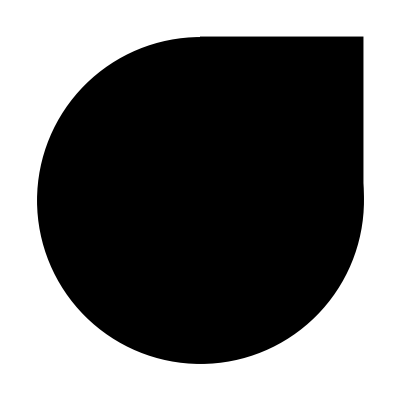

```mathematica
workFunc[Disk[],Rectangle[]]
```

```mathematica
workFunc[Range[1000],Range[45]]
```

workFunc[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45}]

## Functional vs Procedural

Helper function to time the results

```mathematica
SetAttributes[time,HoldAllComplete];
time[any___]:=First[AbsoluteTiming@any];
```

```mathematica
data=Range[10^7];
```

```mathematica
time@Total[#^2&/@data]
```

1.69405

```mathematica
Developer`PackedArrayQ[Prepend[s,1.]]
```

False

```mathematica
time[Plus@@(#^2&/@data)]
```

1.70723

```mathematica
time@Sum[i^2,{i,1,10^7}]
```

0.00542

When performing loops, Do is faster than For, but still slow in WL

```mathematica
time[total=0;For[i=0,i≤Length[data],i++,total+=data[[i]]^2]]
```

20.606

```mathematica
time[total=0;Do[total+=data[[i]]^2,{i,Length[data]}]]
```

9.61197

Not using indexes is still fastest:

```mathematica
time[total=0;Do[total+=i^2,{i,data}]]
```

7.29539

#### Big picture here : Don’t use indices and don’t use For

## Vectorization

If we look back at our program that was the sum of the squares, we can speed up faster still :

```mathematica
time@Total[Power[data,2]]
```

1.47514

This is because Power is listable. Many numeric functions have the listable attribute which allows them to work faster on all of the inputs rather than go back and forth in the evaluator with Map

Sin for example is another listable function:

```mathematica
numericdata=N[data];2;
```

```mathematica
time[Sin/@numericdata]
```

1.04688

```mathematica
time[Sin[numericdata]]
```

0.027217

```mathematica
%%/%
```

38.4642

## PackedArrays

What’s different about the two inputs:

```mathematica
time@Total[Power[Prepend[data,0],2]]
time@Total[Power[Prepend[data,0.],2]]
```

1.52036

4.76316

The difference is that the first is a packed array and the second isn’t:

```mathematica
Developer`PackedArrayQ[Prepend[data,0]]
Developer`PackedArrayQ[Prepend[data,0.]]
```

True

False

A packed array is an internal representation of a list of the same type that can be worked on faster than a list of differing types

What’s a packed array? Basically a tensor that has multiple types stored inside it. Many generative functions return packed arrays

```mathematica
Developer`PackedArrayQ[Range[10]]
```

True

Functions with listable attributes typically don’t unpack when called with the list argument:

```mathematica
Developer`PackedArrayQ[#^2&/@Range[10]]
```

False

```mathematica
Developer`PackedArrayQ[Power[Range[10],2]]
```

True

Packed arrays can be Reals too, so long as it’s entirely Reals:

```mathematica
Developer`PackedArrayQ[N@Range[10]]
Developer`PackedArrayQ[Append[N@Range[10],1.]]
Developer`PackedArrayQ[Append[N@Range[10],1]]
```

True

True

False

Another advantage of working with packed arrays is that they are smaller than normal lists:

```mathematica
ByteCount[Developer`FromPackedArray[Range[10000]]]
ByteCount[Range[10000]]
```

240080

80144

Packed arrays (up to a certain size) contain are approximately 8 bytes long on a 64-bit system, while an unpacked array of numeric exprs is about 24 bytes:

```mathematica
N@ByteCount[Range[1000]]/1000
N@ByteCount[Prepend[Range[1000],0.]]/1000
```

8.304

24.216

Many operations can work with PackedArrays directly without unpacking.

```mathematica
d=Range[100];
d[[3]]=5;
Developer`PackedArrayQ[d]
```

True

You can see what functions unpack an array by turning on a message about it every time it happens:

```mathematica
On["Packing"]
```

```mathematica
Append[Range[100],1.]
```

Developer`FromPackedArray::unpack: Unpacking array in call to HoldForm.

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {100}.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,1.}

Many pattern matching functions will unpack arrays:

```mathematica
DeleteCases[Range[100],3]
```

Developer`FromPackedArray::unpack: Unpacking array in call to HoldForm.

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {100}.

{1,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

If an array gets unpacked, you can always repack it (assuming it’s still all the same type) with ToPackedArray

```mathematica
Developer`PackedArrayQ[Developer`ToPackedArray[DeleteCases[Range[100],3]]]
```

Developer`FromPackedArray::unpack: Unpacking array in call to HoldForm.

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {100}.

True

You can’t however attempt to manually pack an array with conflicting types:

```mathematica
Developer`PackedArrayQ[Developer`ToPackedArray[Prepend[Range[1000],0.]]]
```

False

```mathematica
Off["Packing"]
```

## Compile + friends

"Trying to outsmart a compiler defeats much of the purpose of using one" - Brian Kernighan

```mathematica
cf1=Compile[{{data,_Integer,1}},Total[#^2&/@data]]
```

CompiledFunction[…]

```mathematica
time@cf1@data
```

1.94096

```mathematica
cf2=Compile[{{data,_Integer,1}},Total[#^2&/@data],Parallelization->True]
```

CompiledFunction[…]

```mathematica
time@cf2@data
```

1.90107

```mathematica
cf3=Compile[{{data,_Integer,1}},Total[#^2&/@data],Parallelization->True,CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
time@cf3@data
```

1.76357

```mathematica
cf4=Compile[{{data,_Integer,1}},Total[#^2&/@data],Parallelization->True,CompilationTarget->"C",RuntimeAttributes->{Listable}]
```

CompiledFunction[…]

```mathematica
time@cf4@data
```

1.75144

```mathematica
cf5=Compile[{{data,_Integer,1}},Total@Power[data,2],Parallelization->True,CompilationTarget->"C",RuntimeAttributes->{Listable}]
```

CompiledFunction[…]

```mathematica
time@cf5@data
```

1.57794

Let’s look at another example where compiling can provide good benefits - repeatedly application of a function

```mathematica
rand=RandomReal[]
```

0.783566

```mathematica
time@Nest[Sin,RandomReal[],100000000]
```

2.2795

```mathematica
cn1=Compile[{{init,_Real},{num,_Integer}},Nest[Sin,init,num]]
```

CompiledFunction[…]

```mathematica
time@cn1[rand,100000000]
```

2.30586

Here adding the compile to C speeds up better than WL:

```mathematica
cn2=Compile[{{init,_Real},{num,_Integer}},Nest[Sin,init,num],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
time@cn2[rand,100000000]
```

1.57108

```mathematica
time@%82[rand,100000000]
```

2.31463

```mathematica
time@%88[rand,100000000]
```

1.56755

```mathematica
time@Nest[Sin,rand,100000000]
```

2.27169

## Working with large files

When working with large files out of core, streams are your friend

```mathematica
installerFile="/Users/ijohnson/Downloads/M-OSX-L-11.2.0-5768653.dmg";
```

```mathematica
UnitConvert[N@Quantity[FileByteCount[installerFile],"Bytes"],"Gigabytes"]
```

4.02752 GB

This will certainly fail:

```mathematica
ImportString[installerFile,"Binary"]
```

The smallest size for integer byte values in Mathematica is 8 bytes, so each byte in the file will be stored in RAM as 8 bytes

```mathematica
8UnitConvert[N@Quantity[FileByteCount[installerFile],"Bytes"],"Gigabytes"]
```

32.2202 GB

Sidetrack for new 11.2 feature MemoryAvailable:

```mathematica
Dynamic[Refresh[SystemInformation["Machine","PhysicalFree"],UpdateInterval->0]]
```

-Graphics-

```mathematica
SystemInformation["Machine"]
```

{MemoryAvailable→6.44257 GiB,PhysicalUsed→12.2161 GiB,PhysicalFree→2.32857 GiB,PhysicalTotal→16. GiB,VirtualUsed→17.3003 GiB,VirtualFree→22. GiB,VirtualTotal→22. GiB,PageSize→4096,PageUsed→5.08423 GiB,PageFree→937.75 MiB,PageTotal→6. GiB,AppMemory→7.64988 GiB,Wired→2.05039 GiB,Active→4.9824 GiB,Inactive→4.114 GiB,Compressed→2.51582 GiB,PageIns→50553684,PageOuts→1763513}

You can view memory available with a dynamic palette :

```mathematica
CreatePalette[DynamicModule[{vals={}},Column[{Dynamic[ListLinePlot[vals=Reverse@Take[Reverse[vals],UpTo[300]],Filling->Axis,PlotRange->{0,Max[8,QuantityMagnitude@vals]},ImageSize->Medium]],Dynamic[Refresh[AppendTo[vals,SystemInformation["Machine","PhysicalFree"]]//Last,UpdateInterval->1.5]]},Alignment->Center]]]
```

bq9jg_shm72FrontEndObject[LinkObject["bq9jg_shm", 3, 1]]72Untitled-24

```mathematica
With[{sym=Unique[]},sym=Range[10^8];3;SymbolName[Unevaluated[sym]]]
```

$32

```mathematica
ClearAll[Evaluate[%]]
```

Getting back to large files....

The function to use are Read | ReadList, etc.

```mathematica
strm=OpenRead[installerFile,BinaryFormat->True]
```

InputStream[…]

```mathematica
Read[strm,Byte]
```

66

```mathematica
Read[strm,Byte]
```

90

```mathematica
UnitConvert[Quantity[10000,"Byte"]/Quantity[time@ReadList[strm,Byte,10000],"Seconds"],"Megabytes"/"Seconds"]
```

27.027 MB/s

```mathematica
Table[UnitConvert[Quantity[10000,"Byte"]/Quantity[time@ReadList[strm,Byte,10000],"Seconds"],"Megabytes"/"Seconds"],50]
```

{24.8139 MB/s,21.8818 MB/s,24.3309 MB/s,19.7239 MB/s,25.2525 MB/s,26.2467 MB/s,24.7525 MB/s,28.49 MB/s,25.3165 MB/s,23.9234 MB/s,25.4453 MB/s,24.7525 MB/s,20.4499 MB/s,27.933 MB/s,29.2398 MB/s,28.6533 MB/s,21.1864 MB/s,22.0264 MB/s,22.3714 MB/s,23.4192 MB/s,23.6407 MB/s,26.0417 MB/s,23.4742 MB/s,26.5252 MB/s,23.3645 MB/s,25.8398 MB/s,26.738 MB/s,25.4453 MB/s,26.178 MB/s,25.5102 MB/s,27.3224 MB/s,24.6914 MB/s,17.0358 MB/s,24.3902 MB/s,26.178 MB/s,19.6464 MB/s,26.738 MB/s,27.1739 MB/s,29.4985 MB/s,28.4091 MB/s,20.4499 MB/s,27.5482 MB/s,25.3165 MB/s,26.3158 MB/s,26.178 MB/s,25.4453 MB/s,24.4499 MB/s,25.9067 MB/s,24.9377 MB/s,27.3224 MB/s}

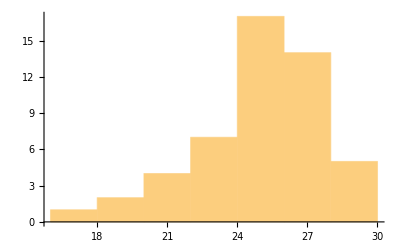

```mathematica
Histogram[%]
```

Specifically when working with large files that aren’t as simple to read with bytes, look into RecordSeparators

```mathematica
SetStreamPosition[strm,0]
```

0

Here we will attempt to find the first instance of the string “ian” in the mathematica installer:

```mathematica
ReadList[strm,Record,1,RecordSeparators->{"ian"}]
```

{6157932}
 |  |  |  |

```mathematica
ReadList[strm,Byte,3]
```

{105,97,110}

```mathematica
FromCharacterCode[%]
```

ian

## Parallelization (the easy way)

```mathematica
ParallelTable
```

```mathematica
ParallelDo
```

```mathematica
ParallelSubmit
```

For more on this come to my next talk on High Performance Computing